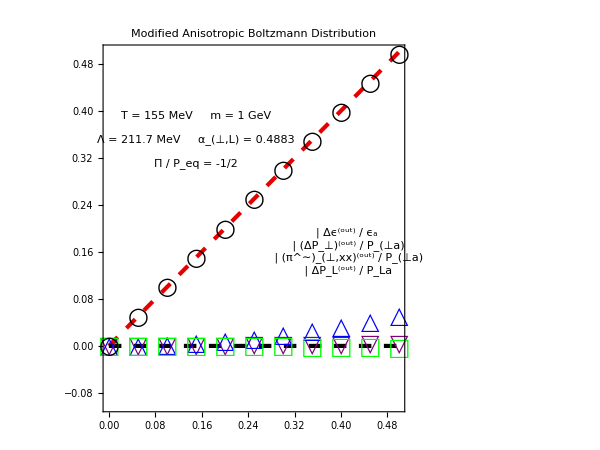

```mathematica
(*MASSIVE ANISOTROPIC BOLTZMANN GAS*)

T0 = 0.155;
mass = 1.0;  (* proton mass scale *)
sign = 0;
αT = 0.48833668933;
αL = 0.48833668933;
Λ = 0.21173838764; (* GeV *)
frac=Table[0.05*i,{i,0,10}];

(*I should plot the PL and PT matching conditions*)
(*As well as the pi_perp_xx*)

Δϵoverϵdata = {0.0,3.7974972*10^-05,0.00015189378,0.00034173809,0.00060747731,0.00094906852,0.0013664564,0.0018595731,0.0024283382,0.0030726585,0.0037924276};

ΔPToverPTdata = {0.0,0.00050381693,0.0020152039,0.0045339693,0.0080597914,0.012592217,0.018130656,0.024674378,0.032222506,0.04077401,0.050327699};

ΔPLoverPLdata = {0.0,-2.6954853*10^-05,-0.00010781729,-0.00024258091,-0.00043123483,-0.00067376337,-0.00097014568,-0.0013203552,-0.0017243589,-0.0021821166,-0.00269358};

piperpoverPTdata = {0.0,0.04999622,0.099969764,0.14989799,0.1997583,0.24952819,0.29918528,0.34870733,0.39807227,0.44725822,0.49624357};

style={Directive[RGBColor[0.9,0,0],AbsoluteThickness[3],AbsoluteDashing[Medium]],Directive[RGBColor[0,0,0],AbsoluteThickness[3],AbsoluteDashing[Medium]]};

legend1=Panel[Grid[{{Graphics[{EdgeForm[Directive[Thick,Purple]],White,Polygon[{{1,Sqrt[3]},{0,0},{-1,Sqrt[3]}}]},ImageSize->16],Style["Δϵ^(out) / ϵ_a",FontSize->14]},{Graphics[{EdgeForm[Directive[Thick,Blue]],White,Polygon[{{1,0},{0,Sqrt[3]},{-1,0}}]},ImageSize->16],Style["(ΔP_⊥)^(out) / P_(⊥a)",FontSize->14]},
{Graphics[{Directive[Thick,Black],Circle[]},ImageSize->16],Style["(π^∼)_(⊥,xx)^(out) / P_(⊥a)",FontSize->14]},{Graphics[{EdgeForm[Directive[Thick,Green]],White,Rectangle[]},ImageSize->16],Style["ΔP_L^(out) / P_La",FontSize->14]}}],Background->White];

legend2=Panel[Grid[{{Style["T = 155 MeV     m = 1 GeV",FontSize->14]},{},
{Style["Λ = 211.7 MeV     α_(⊥,L) = 0.4883",FontSize->14]},{},{Style["Π / P_eq = -1/2",FontSize->14]}}],Background->White];


Δϵoverϵplot = Table[{frac[[i]],Δϵoverϵdata[[i]]},{i,1,Length[frac]}];
ΔPToverPTplot = Table[{frac[[i]],ΔPToverPTdata[[i]]},{i,1,Length[frac]}];
ΔPLoverPLplot  = Table[{frac[[i]],ΔPLoverPLdata [[i]]},{i,1,Length[frac]}];
piperpoverPTplot = Table[{frac[[i]],piperpoverPTdata[[i]]},{i,1,Length[frac]}];

Show[{{
Plot[{x,0.0},{x,0,0.5},PlotRange->{-0.1,0.5},ImageSize->600,PlotStyle->style,Frame->True,Axes->False,BaseStyle->{FontSize->22},AspectRatio->0.75],
ListPlot[{Δϵoverϵplot,ΔPToverPTplot,ΔPLoverPLplot,piperpoverPTplot},PlotRange->{-0.1,0.5},ImageSize->600,Frame->True,Axes->False,PlotMarkers->{{▽,24},{△,24},{□,24},{○,24}},PlotStyle->{Purple,Blue,Green,Black},BaseStyle->{FontSize->22},AspectRatio->0.75]}
},Epilog->{Inset[legend1,{0.41,0.16}],Inset[legend2,{0.15,0.35}]},ImageSize->{600,500},FrameLabel->{"(π^∼)_(⊥,xx)^(in) / P_(⊥a)"},PlotLabel->Style["Modified Anisotropic Boltzmann Distribution",FontSize->22]]
```